# Effet Stark

```mathematica
Clear[]
Off[General::"spell1"]
<<"Units`"
<<"PhysicalConstants`"
$MaxPrecision=150;$MachinePrecision;$MaxExtraPrecision=150;$MaxMachineNumber;
```

### Rb^87 data and other constants

Natural constants

```mathematica
hbar=1.054571596*10^-34; (*Js, ref. Steck*)
Head[hbar];
SetPrecision[hbar,15]; (*to show hbar with 15 numbers*)
Precision[hbar] (*hbar is given in Machine Precision*);
h=hbar*2.*π;
Subscript[μ, 0]=4.*π*10^-7 ; (*N/A^2, exact, ref. Steck*)
c=2.99792458*10^8; (*m/s, exact, ref. Steck*)
Subscript[ϵ, 0]=(Subscript[μ, 0] c^2)^-1; (*F/m, exact, ref. Steck*)
Subscript[k, B]=1.3806503*10^-23 ;(*J/K, ref. Steck*)
Subscript[m, e]=9.10938188*10^-31 (*ElectronMass [kg], ref. Steck*);
Subscript[e, SI]=1.602176462*10^-19 (*ElectronCharge [C], ref. Steck*);
Subscript[e, cgs]=Subscript[e, SI]/(4.π Subscript[ϵ, 0])^(1/2);
Subscript[a, 0]=0.5291772083*10^-10; (*m , Bohr Radius, ref. Steck*)
hbar^2/(Subscript[m, e]*Subscript[e, cgs]^2) (*Subscript[a, 0] calculated*);
Subscript[e, cgs]^2/Subscript[a, 0]/Subscript[e, SI] (*atomic energy unit given in [eV=Subscript[e, SI] V]*)
Subscript[μ, B]=9.27400899*10^-24 ;(*J/T , Bohr Magneton, ref. Steck*)
u=1.66053873*10^-27 ;(*kg, Atomic mass unit , ref. Steck*)
α=Subscript[e, SI]^2/(hbar c 4. π Subscript[ϵ, 0]);
SetPrecision[α,9];
Subscript[R, ∞]=(α^2 Subscript[m, e] c)/(4.π hbar) ;(* Rydberg constant: Wikipedia Subscript[R, ∞]=1.0973731568525(73)*10^7 m^-1, slightly different from value calculated with constants from ref. Steck *) 

SetPrecision[Subscript[R, ∞],13] (*to show Subscript[R, ∞] with 13 numbers*)

(*Rubidium*)

Subscript[m, Rb87]=86.909180520*u; (*kg, Atomic Mass^87 Rb, ref. Steck*)
Subscript[R, Rb87]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb87])^-1 ;(* Subscript[R, Rb]=109736.605 cm^-1 from PRA 67 052502 (2003) Gallagher, "where R_Rb is the Rydberg constant for the reduced electron mass in Rb" -> obviously for Rb85 !! *)
SetPrecision[Subscript[R, Rb87],9] (*to show Subscript[R, ∞] with 9 numbers*)

Subscript[m, Rb85]=84.909180520*u; (*kg, Atomic Mass^85 Rb*)
Subscript[R, Rb85]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb85])^-1 ;
1-(1+Subscript[m, e]/Subscript[m, Rb85])^-1 (*relative effect of reduced mass (replacing Subscript[R, ∞] by Subscript[R, Rb87]) on Energy is in the order of 6E-6*)
Null
```

27.2114

1.09737315688×10^7

1.09736623×10^7

6.46074×10^-6

### Define Functions for calculation of energy-levels without interaction

Quantum defects taken from publication T. Gallagher et al. PRA 67, 052502 (2003), n>20. nf_j and ng_j states are found in Han, Gallagher et al. PRA 74 054502 (2006)

```mathematica
Subscript[δ, 0]={3.1311804,2.6548849,2.6416737,1.34809171,1.34646572,0.0165192,0.0165437,0}
Subscript[δ, 2]={0.1784,0.2900,0.2950,-0.60286,-0.59600,-0.085,-0.086,0};


(*list of quantum defects for Rb85 et Rb87 from PRA 67, 052502 (2003) 1^st entry Subscript[ns, 1/2]: lj=1, 2^nd entry Subscript[np, 1/2]:lj=2,3^nd entry Subscript[np, 3/2]:lj=3, 4^th entry Subscript[nd, 3/2]: lj=4, 5^th entry Subscript[nd, 5/2]:lj=5, 6^th entry Subscript[nf, 5/2]:lj=6, 7^th entry Subscript[nf, 7/2]:lj=7,n>20, 8^th entry for levels with l>f quantum defect is set to zero*)

δ[lj_,n_]:=Subscript[δ, 0][[lj]]+(Subscript[δ, 2][[lj]])/(n-Subscript[δ, 0][[lj]])^2; (*Quantum defect for given lj and n for n>20, see T. Gallagher "Rydberg Atoms"*)
δ[7,41]

(*Energy of Rydberg levels with quantum defect (fine structure)*)

En[lj_,n_]:=-(Subscript[R, Rb87] c)/(n-δ[lj,n])^2 (*[Hz], Energy of Level |n,l,j> with quantum effect and mass correction *)
ERadinte[lj_,n_]:=-(0.5*(1+Subscript[m, e]/Subscript[m, Rb87])^-1)/(n-δ[lj,n])^2 (*[Unit=Atomic Energy Unit = Subscript[e, cgs]^2/Subscript[a, 0] [J] = 2 h Subscript[R, ∞] c [J] = 2*Subscript[E, Hydrogen n=1]], "Energy" as needed by "radinte.exe" of Level |n,l,j> with quantum defect and with reduced mass effect, n>20 *)
(*Effect of mass on Energylevels for Rb^87 and Rb^85*)

Enw85[lj_,n_]:=-(Subscript[R, Rb85] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb85 *)
SetPrecision[(Enw85[1,51]-Enw85[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb85 to control*);
Enw87[lj_,n_]:=-(Subscript[R, Rb87] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb87 *);
SetPrecision[(Enw87[1,51]-Enw87[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb87 to control*);
SetPrecision[(Enw87[1,51]-Enw87[1,50])-(Enw85[1,51]-Enw85[1,50]),15] (* Difference for Transition Frequencies in Hz for Rb87 and Rb85, effect in the order of 10kHz *)
```

{3.13118,2.65488,2.64167,1.34809,1.34647,0.0165192,0.0165437,0}

0.0164925 Null

7597.31420898438

### Integration of C-Code for Numerov Integration to calculate radial matrix elements, Tests of accuracy by comparison to Hydrogen

Install the external program "radinte.exe" which will be used to calculate the radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration in atomic length unit [a_0^I]   with the following Mathematica syntax: "RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer]".  l1 and l2 are magnetic quantum numbers. E1 and E2 are the Energies of the levels |n,l,j> calculated with quantum defect and with mass correction in atomic energy units ([e_cgs)^2/a_0] done by ERadinte[lj_,n_].
Attention: The Real numbers E1 and E2 have to be in floating point representation, otherwise Mathlink (communication between radinte.exe and Mathematica) will hang up!! The calculation in radinte.exe is done in double precision.

```mathematica
Install["D:\\Doktorarbeit\\Simus\\Mathematica\\radinte\\radinte\\Debug\\radinte.exe"]
?RadIntE

(*Test: Comparison with existing .exe file *)
RadIntE[
  ERadinte[1,50],-0.0453211,0,1,1]
RadIntE[-0.0453211,ERadinte[1,50],1,0,1]
RadIntE[-0.03661927,ERadinte[1,50],1,0,1]
Timing[RadIntE[-0.03661928,-0.0002276161,1,0,1]]
```

LinkObject["D:\Documents\raulcteixeira\Documents\Simulations et calculs\Simulation_Rydberg + taille du BEC dans piège magnétique\Spectres VdW\radinte\radinte.exe",18,12]

RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer] calculates radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration.

-0.0267742

-0.0267742

0.00740212

{0.,0.00741686}

## | 58 s1/2 >

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=61;Subscript[l, 1]=60;Subscript[j, 1]=60+1/2;Subscript[m, 1]=60+1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=52; Subscript[n, max]=67;

δf=400*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==Subscript[m, 1],t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
NList
```

-8.84123×10^11

{0.515,Null}

49

{{61,60,121/2,121/2,-8.84123×10^11,1},{62,60,121/2,121/2,-8.55833×10^11,1},{62,61,121/2,121/2,-8.55833×10^11,-1},{62,61,123/2,121/2,-8.55833×10^11,-1},{63,60,121/2,121/2,-8.28879×10^11,1},{63,61,121/2,121/2,-8.28879×10^11,-1},{63,61,123/2,121/2,-8.28879×10^11,-1},{63,62,123/2,121/2,-8.28879×10^11,1},{63,62,125/2,121/2,-8.28879×10^11,1},{64,60,121/2,121/2,-8.03179×10^11,1},{64,61,121/2,121/2,-8.03179×10^11,-1},{64,61,123/2,121/2,-8.03179×10^11,-1},{64,62,123/2,121/2,-8.03179×10^11,1},{64,62,125/2,121/2,-8.03179×10^11,1},{64,63,125/2,121/2,-8.03179×10^11,-1},{64,63,127/2,121/2,-8.03179×10^11,-1},{65,60,121/2,121/2,-7.78656×10^11,1},{65,61,121/2,121/2,-7.78656×10^11,-1},{65,61,123/2,121/2,-7.78656×10^11,-1},{65,62,123/2,121/2,-7.78656×10^11,1},{65,62,125/2,121/2,-7.78656×10^11,1},{65,63,125/2,121/2,-7.78656×10^11,-1},{65,63,127/2,121/2,-7.78656×10^11,-1},{65,64,127/2,121/2,-7.78656×10^11,1},{65,64,129/2,121/2,-7.78656×10^11,1},{66,60,121/2,121/2,-7.55239×10^11,1},{66,61,121/2,121/2,-7.55239×10^11,-1},{66,61,123/2,121/2,-7.55239×10^11,-1},{66,62,123/2,121/2,-7.55239×10^11,1},{66,62,125/2,121/2,-7.55239×10^11,1},{66,63,125/2,121/2,-7.55239×10^11,-1},{66,63,127/2,121/2,-7.55239×10^11,-1},{66,64,127/2,121/2,-7.55239×10^11,1},{66,64,129/2,121/2,-7.55239×10^11,1},{66,65,129/2,121/2,-7.55239×10^11,-1},{66,65,131/2,121/2,-7.55239×10^11,-1},{67,60,121/2,121/2,-7.32863×10^11,1},{67,61,121/2,121/2,-7.32863×10^11,-1},{67,61,123/2,121/2,-7.32863×10^11,-1},{67,62,123/2,121/2,-7.32863×10^11,1},{67,62,125/2,121/2,-7.32863×10^11,1},{67,63,125/2,121/2,-7.32863×10^11,-1},{67,63,127/2,121/2,-7.32863×10^11,-1},{67,64,127/2,121/2,-7.32863×10^11,1},{67,64,129/2,121/2,-7.32863×10^11,1},{67,65,129/2,121/2,-7.32863×10^11,-1},{67,65,131/2,121/2,-7.32863×10^11,-1},{67,66,131/2,121/2,-7.32863×10^11,1},{67,66,133/2,121/2,-7.32863×10^11,1}}

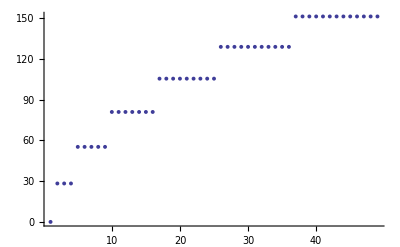

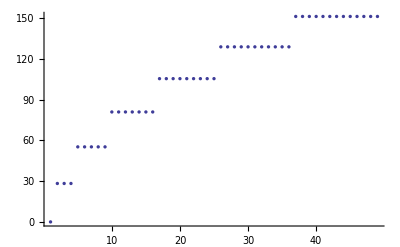

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

```mathematica
Calcul des éléments de matrice non-diagonaux
```

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);



EMatrixelement[{60,0,1/2,1/2},{58,1,1/2,-1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]
```

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{160.498,0.-160.498 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{121/2, 121/2}, {1, -1}, {121/2, -121/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{121/2, 121/2}, {1, 1}, {121/2, -121/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{121/2, 121/2}, {1, -1}, {121/2, -121/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{62, 1/2, 125/2}, {121/2, 1, 61}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{125/2, 121/2}, {1, -1}, {121/2, -121/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{125/2, 121/2}, {1, 1}, {121/2, -121/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{125/2, 121/2}, {1, -1}, {121/2, -121/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{62, 1/2, 125/2}, {121/2, 1, 61}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{2.855,Null}

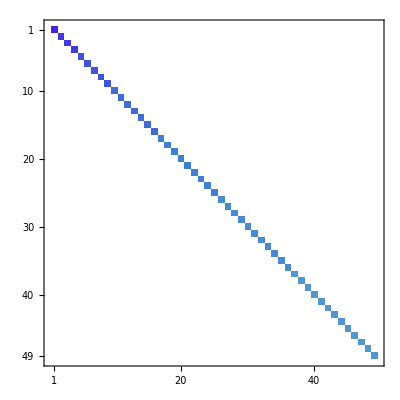

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

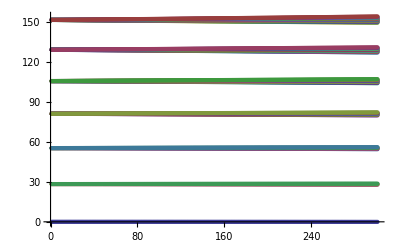

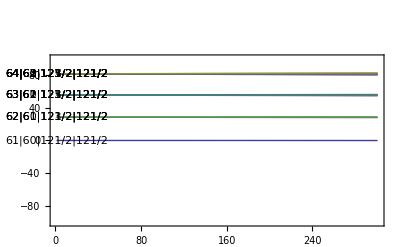

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=1;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList;

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

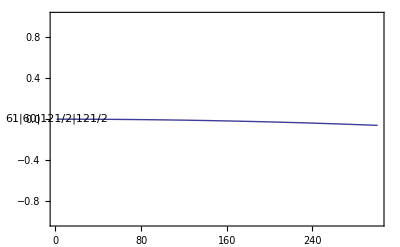

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
LabelList[[1]]
LabelList


MPList[[1]]

Export["61circular_stark_Shift.dat",MPList[[1]]]
```

61|60|121/2|121/2

{61|60|121/2|121/2,62|60|121/2|121/2,62|61|121/2|121/2,62|61|123/2|121/2,63|60|121/2|121/2,63|61|121/2|121/2,63|61|123/2|121/2,63|62|123/2|121/2,63|62|125/2|121/2,64|60|121/2|121/2,64|61|121/2|121/2,64|61|123/2|121/2,64|62|123/2|121/2,64|62|125/2|121/2,64|63|125/2|121/2,64|63|127/2|121/2,65|60|121/2|121/2,65|61|121/2|121/2,65|61|123/2|121/2,65|62|123/2|121/2,65|62|125/2|121/2,65|63|125/2|121/2,65|63|127/2|121/2,65|64|127/2|121/2,65|64|129/2|121/2,66|60|121/2|121/2,66|61|121/2|121/2,66|61|123/2|121/2,66|62|123/2|121/2,66|62|125/2|121/2,66|63|125/2|121/2,66|63|127/2|121/2,66|64|127/2|121/2,66|64|129/2|121/2,66|65|129/2|121/2,66|65|131/2|121/2,67|60|121/2|121/2,67|61|121/2|121/2,67|61|123/2|121/2,67|62|123/2|121/2,67|62|125/2|121/2,67|63|125/2|121/2,67|63|127/2|121/2,67|64|127/2|121/2,67|64|129/2|121/2,67|65|129/2|121/2,67|65|131/2|121/2,67|66|131/2|121/2,67|66|133/2|121/2}

{{1,-6.64938×10^-7},{2,-2.65975×10^-6},{3,-5.98444×10^-6},{4,-0.000010639},{5,-0.0000166234},{6,-0.0000239378},{7,-0.0000325819},{8,-0.000042556},{9,-0.00005386},{10,-0.0000664938},{11,-0.0000804575},{12,-0.000095751},{13,-0.000112374},{14,-0.000130328},{15,-0.000149611},{16,-0.000170224},{17,-0.000192167},{18,-0.00021544},{19,-0.000240043},{20,-0.000265975},{21,-0.000293238},{22,-0.00032183},{23,-0.000351752},{24,-0.000383005},{25,-0.000415587},{26,-0.000449498},{27,-0.00048474},{28,-0.000521312},{29,-0.000559214},{30,-0.000598445},{31,-0.000639006},{32,-0.000680898},{33,-0.000724119},{34,-0.00076867},{35,-0.000814551},{36,-0.000861762},{37,-0.000910302},{38,-0.000960173},{39,-0.00101137},{40,-0.0010639},{41,-0.00111776},{42,-0.00117295},{43,-0.00122947},{44,-0.00128732},{45,-0.0013465},{46,-0.00140701},{47,-0.00146885},{48,-0.00153202},{49,-0.00159652},{50,-0.00166235},{51,-0.00172951},{52,-0.001798},{53,-0.00186782},{54,-0.00193897},{55,-0.00201145},{56,-0.00208526},{57,-0.0021604},{58,-0.00223687},{59,-0.00231467},{60,-0.0023938},{61,-0.00247425},{62,-0.00255604},{63,-0.00263916},{64,-0.00272361},{65,-0.00280939},{66,-0.0028965},{67,-0.00298494},{68,-0.0030747},{69,-0.0031658},{70,-0.00325823},{71,-0.00335199},{72,-0.00344708},{73,-0.0035435},{74,-0.00364124},{75,-0.00374032},{76,-0.00384073},{77,-0.00394247},{78,-0.00404554},{79,-0.00414994},{80,-0.00425566},{81,-0.00436272},{82,-0.00447111},{83,-0.00458083},{84,-0.00469188},{85,-0.00480425},{86,-0.00491796},{87,-0.005033},{88,-0.00514937},{89,-0.00526707},{90,-0.0053861},{91,-0.00550645},{92,-0.00562814},{93,-0.00575116},{94,-0.00587551},{95,-0.00600119},{96,-0.0061282},{97,-0.00625653},{98,-0.0063862},{99,-0.0065172},{100,-0.00664953},{101,-0.00678319},{102,-0.00691818},{103,-0.0070545},{104,-0.00719214},{105,-0.00733112},{106,-0.00747143},{107,-0.00761307},{108,-0.00775604},{109,-0.00790034},{110,-0.00804597},{111,-0.00819293},{112,-0.00834122},{113,-0.00849084},{114,-0.00864179},{115,-0.00879407},{116,-0.00894768},{117,-0.00910262},{118,-0.00925889},{119,-0.00941649},{120,-0.00957542},{121,-0.00973568},{122,-0.00989727},{123,-0.0100602},{124,-0.0102244},{125,-0.01039},{126,-0.0105569},{127,-0.0107252},{128,-0.0108948},{129,-0.0110657},{130,-0.0112379},{131,-0.0114114},{132,-0.0115863},{133,-0.0117626},{134,-0.0119401},{135,-0.012119},{136,-0.0122992},{137,-0.0124808},{138,-0.0126636},{139,-0.0128478},{140,-0.0130334},{141,-0.0132202},{142,-0.0134084},{143,-0.013598},{144,-0.0137888},{145,-0.013981},{146,-0.0141745},{147,-0.0143694},{148,-0.0145655},{149,-0.014763},{150,-0.0149619},{151,-0.015162},{152,-0.0153635},{153,-0.0155664},{154,-0.0157705},{155,-0.015976},{156,-0.0161828},{157,-0.016391},{158,-0.0166005},{159,-0.0168113},{160,-0.0170234},{161,-0.0172369},{162,-0.0174517},{163,-0.0176678},{164,-0.0178853},{165,-0.0181041},{166,-0.0183242},{167,-0.0185456},{168,-0.0187684},{169,-0.0189925},{170,-0.019218},{171,-0.0194448},{172,-0.0196729},{173,-0.0199023},{174,-0.0201331},{175,-0.0203652},{176,-0.0205986},{177,-0.0208333},{178,-0.0210694},{179,-0.0213068},{180,-0.0215456},{181,-0.0217857},{182,-0.0220271},{183,-0.0222698},{184,-0.0225139},{185,-0.0227593},{186,-0.023006},{187,-0.0232541},{188,-0.0235035},{189,-0.0237542},{190,-0.0240063},{191,-0.0242596},{192,-0.0245143},{193,-0.0247704},{194,-0.0250278},{195,-0.0252865},{196,-0.0255465},{197,-0.0258079},{198,-0.0260706},{199,-0.0263346},{200,-0.0266},{201,-0.0268667},{202,-0.0271347},{203,-0.027404},{204,-0.0276747},{205,-0.0279467},{206,-0.0282201},{207,-0.0284947},{208,-0.0287707},{209,-0.0290481},{210,-0.0293267},{211,-0.0296067},{212,-0.0298881},{213,-0.0301707},{214,-0.0304547},{215,-0.03074},{216,-0.0310267},{217,-0.0313147},{218,-0.031604},{219,-0.0318946},{220,-0.0321866},{221,-0.0324799},{222,-0.0327745},{223,-0.0330705},{224,-0.0333678},{225,-0.0336664},{226,-0.0339664},{227,-0.0342677},{228,-0.0345703},{229,-0.0348742},{230,-0.0351795},{231,-0.0354861},{232,-0.0357941},{233,-0.0361033},{234,-0.0364139},{235,-0.0367259},{236,-0.0370391},{237,-0.0373537},{238,-0.0376697},{239,-0.0379869},{240,-0.0383055},{241,-0.0386254},{242,-0.0389467},{243,-0.0392693},{244,-0.0395932},{245,-0.0399184},{246,-0.040245},{247,-0.0405729},{248,-0.0409021},{249,-0.0412327},{250,-0.0415646},{251,-0.0418978},{252,-0.0422324},{253,-0.0425683},{254,-0.0429055},{255,-0.0432441},{256,-0.043584},{257,-0.0439252},{258,-0.0442677},{259,-0.0446116},{260,-0.0449568},{261,-0.0453034},{262,-0.0456512},{263,-0.0460004},{264,-0.046351},{265,-0.0467028},{266,-0.047056},{267,-0.0474106},{268,-0.0477664},{269,-0.0481236},{270,-0.0484821},{271,-0.048842},{272,-0.0492032},{273,-0.0495657},{274,-0.0499295},{275,-0.0502947},{276,-0.0506612},{277,-0.0510291},{278,-0.0513982},{279,-0.0517687},{280,-0.0521406},{281,-0.0525137},{282,-0.0528882},{283,-0.0532641},{284,-0.0536412},{285,-0.0540197},{286,-0.0543995},{287,-0.0547807},{288,-0.0551632},{289,-0.055547},{290,-0.0559321},{291,-0.0563186},{292,-0.0567064},{293,-0.0570956},{294,-0.057486},{295,-0.0578778},{296,-0.058271},{297,-0.0586655},{298,-0.0590613},{299,-0.0594584},{300,-0.0598568},{301,-0.0602566}}

61circular_stark_Shift.dat